```mathematica
<<QCDLib`;
```

Loaded QCDLib`util` with symbols: {addQuad,arrayReshape,cache,cacheable,CacheDir,comm,coordMod,deepEq,dumpGlobalFns,exportRel,fname,getOptsFor,makeEvalSupp,mmaColors,mmaPlotMarkers,nanToZero,ones,readRel,relPath,symbolsWithDownValues,symmMat,wrap,writeRel}

Loaded QCDLib`plot` with symbols: {bigErrBarFn,constFitEpilog,errorListLogPlot,frameOpts,title}

Loaded QCDLib`visualize` with symbols: {draw2DLogmags,draw2DPhases,draw2DResids,drawpath}

Loaded QCDLib`analyze` with symbols: {autocorrs,bootstrap,constantFit,constantSysFit,getMeffs,meff,stdDev}

Loaded QCDLib`sn` with symbols: {getCSCO,getCSCOSubspace,getTabxRep,getTabxShape,getTabxTabList,getYamanouchiSymbol,PermRep,regularTabxShapeQ,toGraphics,YoungTab,YoungTabx}

Loaded QCDLib`phase` with symbols: {get2DResids}

```mathematica
<<ErrorBarPlots`;
```

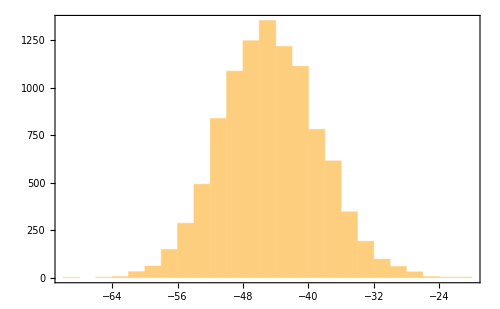

```mathematica
Module[{actions},
actions = readRel["b1.0_N10000_100.S.dat", "Real64"];
Print@Histogram[actions, frameOpts[]];
];
```

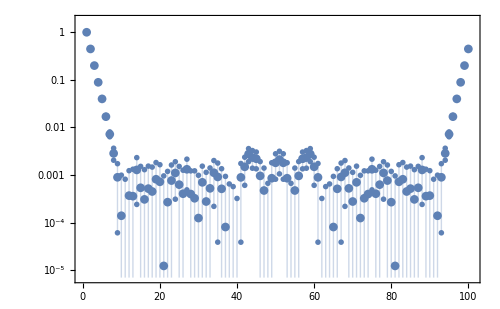

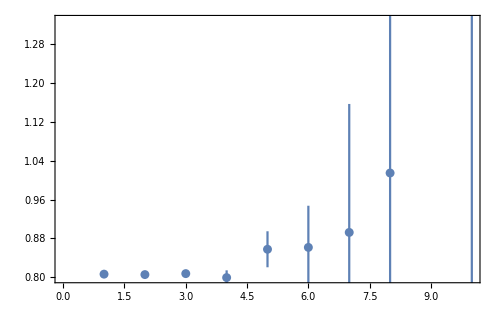

```mathematica
Module[{Ncfg, L, cfgs, corrs, corr, mass},
Ncfg =10000; L = 100;
cfgs = arrayReshape[
readRel["b1.0_N10000_100.dat", "Real64"],
{Ncfg, L}];
(*Print@ListPlot[cfgs⟦1⟧, Joined->True, frameOpts[]];*)
corrs = Transpose@Table[Total[Cos[cfgs - RotateLeft[cfgs, {0,-t}]], {2}]/L, {t, 0, L-1}];
corr = bootstrap[corrs, 100, Mean];
mass = bootstrap[corrs, 100, meff];
Print@errorListLogPlot[Transpose@corr, frameOpts[]];
Print@ErrorListPlot[Transpose[mass]⟦;;10⟧, frameOpts[]];
];
```